Michael Barile
785
Heimholtz equation

Parameters

depth of water, set at 1 unit

Analysis

We first construct an unperturbed grid of 400 triangular elements and 231 nodes.  We then use the RandomReal function to slightly perturb the interior nodes of the grid.  The perturbed grid is displayed.  After determining the degree 1 polynomials dual to the nodes of the reference element via Vandermonde, we define the element basis polynomials as functions of the vertices of the element triangle and x and y using the affine transformation and inverse as described in the text.  We then determine the relevant integrals for entries in the global K and M matrices as functions of the element vertices ( pg.31-32 of text).  Once this is done, we assemble the global K and M matrices and apply the Dirichlet boundary condition to both so that λ = 1 will be an eigenvalue of M^-1 K.   Finally, we solve using the Eigensystem function, which produces 231 eigenvalues and eigenvectors (the same as the number of nodes).  We select 3 eigenvalues, one in the mid-range, one large and one small.  The associated eigenvectors provide our z-coordinates at the nodes.  We see that the mid-range eigenvalue produces a reasonable looking result, while the large eigenvalue is choppier.  The smallest eigenvalue produces a much smoother result than the other two.

Geometric Model

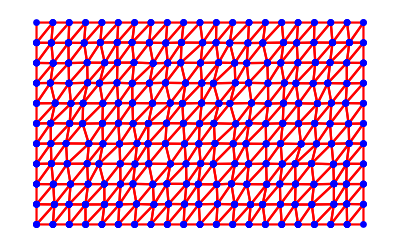

```mathematica
(* constructing unperturbed grid *)

Δx=5;
Δy=5;

grid={};
For[i=1,i≤21,++i,
xyInit={Δx*(i-1),0.};
AppendTo[grid,xyInit];
For[j=2,j≤11,++j,
AppendTo[grid,{xyInit[[1]],grid[[j-1]][[2]]+Δy}]
];
];

(* assembling Pool Nodes list *)

PoolNodes={};
For[i=1,i<=Length[grid],++i,
AppendTo[PoolNodes,{i,grid[[i]][[1]],grid[[i]][[2]]}]
];

(* assembling Pool Elements list *)

PoolElems={};
For[i=1,i≤Length[PoolNodes]-11,++i,
If[Mod[i,11]==0,
,
AppendTo[PoolElems,{i,i+11,i+12}];
AppendTo[PoolElems,{i,i+12,i+1}];
];
];

For[i=1,i≤400,++i,
PoolElems[[i]]=Prepend[PoolElems[[i]],i]
];

(* perturbing inner nodes *)

PoolNodesPert={};
For[i=1,i≤Length[PoolNodes],++i,
If[i≤11||i≥221||Mod[i,11]==0||Mod[i,11]==1,
AppendTo[PoolNodesPert,PoolNodes[[i]]],
AppendTo[PoolNodesPert,{i,PoolNodes[[i]][[2]]+RandomReal[{-1,1}],PoolNodes[[i]][[3]]+RandomReal[{-.08,.08}]}];
];
];

PoolNodes=PoolNodesPert;

(* constructing triangulated, perturbed grid *)

elems={};
For[i=1,i≤Length[PoolElems],++i,
elemList={};
For[j=2,j≤4,++j,
AppendTo[elemList,{PoolNodes[[PoolElems[[i]][[j]]]][[2]],PoolNodes[[PoolElems[[i]][[j]]]][[3]]}];
];
AppendTo[elemList,elemList[[1]]
];
AppendTo[elems,elemList]
];

grid=ListPlot[elems,PlotStyle->Red,Joined->True,PlotMarkers->Graphics[{Blue,Thick,Disk[]},ImageSize->7],Axes->False]
```

Polynomial Model

```mathematica
(* reference element and Vandermonde *)
mat={{1,0,0},{1,1,0},{1,0,1}};
MatrixForm[mat];
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};
coef1=LinearSolve[mat,e1]
coef2=LinearSolve[mat,e2]
coef3=LinearSolve[mat,e3]
```

{1,-1,-1}

{0,1,0}

{0,0,1}

```mathematica
(* degree 1 polynomials dual to nodes of reference element, triangle with Subscript[v, 1]=(0,0), Subscript[v, 2]=(1,0), Subscript[v, 3]=(0,1)*)
Subscript[p, 1][x_,y_]:=1-x-y;
Subscript[p, 2][x_,y_]:=x;
Subscript[p, 3][x_,y_]:=y;
```

```mathematica
(* linear transformation followed by translation mapping reference triangle to element triangle, as well as inverse mapping *)
transformMat[α_,β_,γ_,δ_,μ_,ν_]:={{γ-α,μ-α},{δ-β,ν-β}};
translateMat[α_,β_]:={α,β};
inverseTransformMat[α_,β_,γ_,δ_,μ_,ν_]:=Inverse[transformMat[α,β,γ,δ,μ,ν]];aMat[α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=transformMat[α,β,γ,δ,μ,ν].{x,y}+translateMat[α,β];
aMatInv[α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=inverseTransformMat[α,β,γ,δ,μ,ν].({x,y}-translateMat[α,β]);
```

```mathematica
(* element basis polynomials as a function of vertices of element triangle and x,y. *)
Subscript[p, 1,e][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=Subscript[p, 1][aMatInv[α,β,γ,δ,μ,ν,x,y][[1]],aMatInv[α,β,γ,δ,μ,ν,x,y][[2]]];
Subscript[p, 2,e][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=(1/Det[transformMat[α,β,γ,δ,μ,ν]])*((ν-β)*x+(α-μ)*y+β*μ-α*ν);
Subscript[p, 3,e][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=(1/Det[transformMat[α,β,γ,δ,μ,ν]])*((β-δ)*x+(γ-α)*y+α*δ-β*γ);
```

```mathematica
(* Integral formulas for calculating entries of M *)
intMeq[α_,β_,γ_,δ_,μ_,ν_]:=Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]/12;
intMnoteq[α_,β_,γ_,δ_,μ_,ν_]:=Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]/24;
```

```mathematica
(* Integral formulas for calculating entries of K *)
Subscript[intK, 1,1][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=((D[Subscript[p, 1,e][α,β,γ,δ,μ,ν,x,y],x])^2+(D[Subscript[p, 1,e][α,β,γ,δ,μ,ν,x,y],y])^2)/(2*Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]);
Subscript[intK, 2,2][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=((D[Subscript[p, 2,e][α,β,γ,δ,μ,ν,x,y],x])^2+(D[Subscript[p, 2,e][α,β,γ,δ,μ,ν,x,y],y])^2)/(2*Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]);
Subscript[intK, 3,3][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=((D[Subscript[p, 3,e][α,β,γ,δ,μ,ν,x,y],x])^2+(D[Subscript[p, 3,e][α,β,γ,δ,μ,ν,x,y],y])^2)/(2*Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]);
Subscript[intK, 1,2][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=((D[Subscript[p, 1,e][α,β,γ,δ,μ,ν,x,y],x]*D[Subscript[p, 2,e][α,β,γ,δ,μ,ν,x,y],x])+(D[Subscript[p, 1,e][α,β,γ,δ,μ,ν,x,y],y]*D[Subscript[p, 2,e][α,β,γ,δ,μ,ν,x,y],y]))/(2*Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]);
Subscript[intK, 2,1][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=((D[Subscript[p, 1,e][α,β,γ,δ,μ,ν,x,y],x]*D[Subscript[p, 2,e][α,β,γ,δ,μ,ν,x,y],x])+(D[Subscript[p, 1,e][α,β,γ,δ,μ,ν,x,y],y]*D[Subscript[p, 2,e][α,β,γ,δ,μ,ν,x,y],y]))/(2*Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]);
Subscript[intK, 1,3][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=((D[Subscript[p, 1,e][α,β,γ,δ,μ,ν,x,y],x]*D[Subscript[p, 3,e][α,β,γ,δ,μ,ν,x,y],x])+(D[Subscript[p, 1,e][α,β,γ,δ,μ,ν,x,y],y]*D[Subscript[p, 3,e][α,β,γ,δ,μ,ν,x,y],y]))/(2*Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]);
Subscript[intK, 3,1][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=((D[Subscript[p, 1,e][α,β,γ,δ,μ,ν,x,y],x]*D[Subscript[p, 3,e][α,β,γ,δ,μ,ν,x,y],x])+(D[Subscript[p, 1,e][α,β,γ,δ,μ,ν,x,y],y]*D[Subscript[p, 3,e][α,β,γ,δ,μ,ν,x,y],y]))/(2*Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]);
Subscript[intK, 2,3][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=((D[Subscript[p, 2,e][α,β,γ,δ,μ,ν,x,y],x]*D[Subscript[p, 3,e][α,β,γ,δ,μ,ν,x,y],x])+(D[Subscript[p, 2,e][α,β,γ,δ,μ,ν,x,y],y]*D[Subscript[p, 3,e][α,β,γ,δ,μ,ν,x,y],y]))/(2*Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]);
Subscript[intK, 3,2][α_,β_,γ_,δ_,μ_,ν_,x_,y_]:=((D[Subscript[p, 2,e][α,β,γ,δ,μ,ν,x,y],x]*D[Subscript[p, 3,e][α,β,γ,δ,μ,ν,x,y],x])+(D[Subscript[p, 2,e][α,β,γ,δ,μ,ν,x,y],y]*D[Subscript[p, 3,e][α,β,γ,δ,μ,ν,x,y],y]))/(2*Abs[Det[transformMat[α,β,γ,δ,μ,ν]]]);
```

Global Matrices K and M

```mathematica
(* initializing global K and global M matrices with zero entries *)

globalK=IdentityMatrix[Length[PoolNodes]]-IdentityMatrix[Length[PoolNodes]];
globalM=IdentityMatrix[Length[PoolNodes]]-IdentityMatrix[Length[PoolNodes]];

(* assembling global K matrix *)

For[i=1,i≤Length[PoolElems],++i,
α=PoolNodes[[PoolElems[[i]][[2]]]][[2]];
β=PoolNodes[[PoolElems[[i]][[2]]]][[3]];
γ=PoolNodes[[PoolElems[[i]][[3]]]][[2]];
δ=PoolNodes[[PoolElems[[i]][[3]]]][[3]];
μ=PoolNodes[[PoolElems[[i]][[4]]]][[2]];
ν=PoolNodes[[PoolElems[[i]][[4]]]][[3]];
For[j=1,j≤3,++j,
For[k=1,k≤3,++k,
globalK[[PoolElems[[i]][[k+1]]]][[PoolElems[[i]][[j+1]]]]=globalK[[PoolElems[[i]][[k+1]]]][[PoolElems[[i]][[j+1]]]]+Subscript[intK, k,j][α,β,γ,δ,μ,ν,x,y]
];
];
];
```

```mathematica
(* assembling global M matrix *)

For[i=1,i≤Length[PoolElems],++i,
α=PoolNodes[[PoolElems[[i]][[2]]]][[2]];
β=PoolNodes[[PoolElems[[i]][[2]]]][[3]];
γ=PoolNodes[[PoolElems[[i]][[3]]]][[2]];
δ=PoolNodes[[PoolElems[[i]][[3]]]][[3]];
μ=PoolNodes[[PoolElems[[i]][[4]]]][[2]];
ν=PoolNodes[[PoolElems[[i]][[4]]]][[3]];
For[j=1,j≤3,++j,
For[k=1,k≤3,++k,
If[k==j,
globalM[[PoolElems[[i]][[k+1]]]][[PoolElems[[i]][[j+1]]]]=globalM[[PoolElems[[i]][[k+1]]]][[PoolElems[[i]][[j+1]]]]+intMeq[α,β,γ,δ,μ,ν],
globalM[[PoolElems[[i]][[k+1]]]][[PoolElems[[i]][[j+1]]]]=globalM[[PoolElems[[i]][[k+1]]]][[PoolElems[[i]][[j+1]]]]+intMnoteq[α,β,γ,δ,μ,ν]
];
];
];
];
```

```mathematica
(* row vector for boundary condition *)
e1={};
For[i=1,i≤Length[PoolNodes],++i,
If[i==1,
AppendTo[e1,1],
AppendTo[e1,0]
];
];
```

```mathematica
(* substituting e1 as defined above into first rows of global K and global M matrices *)

globalK[[1]]=e1;
globalM[[1]]=e1;
```

Finding eigenvalues and eigenvectors and Graphic Display

```mathematica
(* medium eigenvalue *)
Subscript[λ, 1]=Eigensystem[Inverse[globalM].globalK][[1]][[150]]; 
Subscript[eigenVec, 1]=Eigensystem[Inverse[globalM].globalK][[2]][[150]]; 

(* large eigenvalue *)
Subscript[λ, 2]=Eigensystem[Inverse[globalM].globalK][[1]][[10]]; 
Subscript[eigenVec, 2]=Eigensystem[Inverse[globalM].globalK][[2]][[10]]; 

(* small eigenvalue *)
Subscript[λ, 3]=Eigensystem[Inverse[globalM].globalK][[1]][[225]]; 
Subscript[eigenVec, 3]=Eigensystem[Inverse[globalM].globalK][[2]][[225]];
```

```mathematica
(* assembling lists for display *)

listEigenvalue1={};
For[i=1,i≤Length[Subscript[eigenVec, 1]],++i,
AppendTo[listEigenvalue1,{PoolNodes[[i]][[2]],PoolNodes[[i]][[3]],Subscript[eigenVec, 1][[i]]}]
];

listEigenvalue2={};
For[i=1,i≤Length[Subscript[eigenVec, 2]],++i,
AppendTo[listEigenvalue2,{PoolNodes[[i]][[2]],PoolNodes[[i]][[3]],Subscript[eigenVec, 2][[i]]}]
];

listEigenvalue3={};
For[i=1,i≤Length[Subscript[eigenVec, 3]],++i,
AppendTo[listEigenvalue3,{PoolNodes[[i]][[2]],PoolNodes[[i]][[3]],Subscript[eigenVec, 3][[i]]}]
];
```

```mathematica
(* displaying results *)

ListPlot3D[listEigenvalue1,PlotRange->{{0,100},{0,50},{-.3,.3}}]
Print["eigenvalue 1, medium: ",Subscript[λ, 1]]

ListPlot3D[listEigenvalue2,PlotRange->{{0,100},{0,50},{-.3,.3}}]
Print["eigenvalue 2, large: ",Subscript[λ, 2]]

ListPlot3D[listEigenvalue3,PlotRange->{{0,100},{0,50},{-.3,.3}}]
Print["eigenvalue 3, small: ",Subscript[λ, 3]]
```

-Graphics3D-

eigenvalue 1, medium: 0.000424396

-Graphics3D-

eigenvalue 2, large: 0.00193957

-Graphics3D-

eigenvalue 3, small: 0.0000149559